# Analys med Mathematica

I denna notebook jobbar vi med att undersöka funktioner och att rita grafer.

## 1. Invers till en funktion

Låt oss undersöka f(x)=x+sin(x) på intervallet [0,π/2].

```mathematica
f[x_]:=x+Sin[x];
Plot[f[x],{x,0,Pi/2},AspectRatio->Automatic]
```

Funktionen är växande på detta intervall, så den har en invers. Vi kan numeriskt skapa en lista med punkter, (x,f(x)) som ligger på grafen.
Vi kan sedan plotta dessa punkter, och ser att de bildar samma kurva som plotten ovan.

```mathematica
(* Detta skapar en lista med punkter, där vi 'samplar' funktionen på intervall med längden 0.001. Det är lite drygt 1500 punkter. *)
fPoints=Table[{x,f[x]},{x,0,Pi/2,0.001}];
fGraph=ListPlot[fPoints,AspectRatio->Automatic]
```

Den inversen till f(x) skickar f(x) på x, så vi kan approximera denna genom att byta plats på x och y-koordinaterna.

```mathematica
fInvPoints=Table[{f[x],x},{x,0,Pi/2,0.001}];
fInvGraph=ListPlot[fInvPoints,AspectRatio->Automatic]
```

```mathematica
(* Rita punkt-approximationen för f, samt dess invers. *)
Show[fGraph,fInvGraph,PlotRange->All]
```

Vi kan nu slutligen göra om listan med punkter till en interpolerad funktion,
dvs. en funktion som är en anpassning till punkterna. Vi kan sedan använda detta som en vanlig funktion, definierad på intervallet [0,1+Pi/2].

```mathematica
fInv=Interpolation[fInvPoints];
fInv[0.5]
```

```mathematica
(* Det går att numeriskt integrera den inversa funktionen *)
Integrate[fInv[x],{x,0,0.5}]
```

Sammansättningen av en funktion och dess invers ska ju bli x, och detta kan vi kontrollera genom att plotta sammansättningen:

```mathematica
Plot[f[fInv[x]],{x,0,Pi/2+1},AspectRatio->Automatic]
```

## 2. Extrempunkter till en funktion

Genom att plotta en funktion, kan vi enkelt hitta extrempunkterna. Man kan ändra intervallet där funktionen plottas, för att se det lokala beteendet.

```mathematica
Clear[f];
f[x_]:=2.1+1.5x-1.23 x^2+(x^3)/3;
Plot[f[x],{x,0,4}]
Plot[f[x],{x,1.1,1.6}]
```

I detta fall kan man derivera funktionen och se var derivatan är noll, men för mer komplicerade funktioner kan man inte hitta alla nollställen till derivatan.

## 3. Lösning av ekvationer numeriskt

Låt oss försöka hitta alla rötter till derivatan till funktionen w(x) nedan på intervallet [0,π/2].

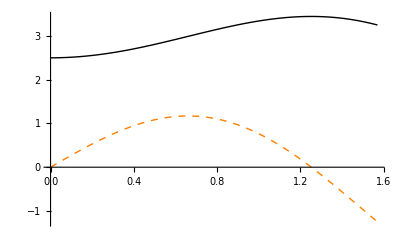

```mathematica
w[x_]:=2 (Sin[x])^2+(5/2) (Cos[x/2])^2;
(* Vi ritar funktionen samt dess derivata. Man kan specificera stilen på graferna med PlotStyle *)
Plot[{w[x],w'[x]},{x,0,Pi/2},PlotStyle->{{Thick,Black},{Thick,Dashed,Orange}}]
```

På figuren ser vi att när x är nära 1.2, så har derivatan ett nollställe. Kommandot FindRoot kan då användas,
för att utgå ifrån 1.2 och leta efter en rot i närheten av detta värde för x.

```mathematica
FindRoot[ w'[x]==0,{x,1.2}]
```

{x→1.25297}

Sätt in detta värde i w’(x), och verifiera att detta är nära 0.

## 4. En dynamisk tangent

Låt oss rita tangenten till en funktion h(x), för ett värde på x=a, där vi kan variera a.
Tangenten är ju en funktion i x, men vi får ju en tangent genom (a,f(a)) för varje värde på parametern a.

```mathematica
h[x_]:=Sin[x]+0.3*Sin[3x];
tangent[a_,x_]:=h[a]+h'[a](x-a);
(* Plotta funktionen samt tangenten vid x=2.3 *)
Plot[{h[x],tangent[2.3,x]},{x,0,6}]
```

Man kan skapa interaktiva bilder också, där bilden uppdateras då en parameter ändras . Vi använder kommandot Manipulate för  detta ändamål.

```mathematica
Manipulate[
Plot[{h[x],tangent[a,x]},{x,0,6},{AspectRatio->Automatic,PlotRange->{{0,6},{-2,2}}}]
,{a,0,6}]
```

## 5. Integraler

Vi kan enkelt hitta primitiva funktioner i Mathematica, med hjälp av Integrate.
Definita integraler, på ett intervall kan också beräknas. Vill vi integrera på ett oändligt intervall, används Infinity.

```mathematica
Integrate[1/(x^2+1)^2,x]
Integrate[1/(x^2+1)^2,{x,0,Infinity}]
```

Vissa funktioner har inte en primitiv funktion som kan uttryckas med elementära funktioner, och Mathematica gör ingen förenkling.
Man kan då istället försöka med numerisk integration, där ett approximativt värde beräknas. Numerisk integration (som bara fungerar på ett intervall) görs medhjälp av NIntegrate.

```mathematica
Integrate[Sin[Cos[x^3]],{x,0,1}]
NIntegrate[Sin[Cos[x^3]],{x,0,1}]
```

Man kan lägga till extra antaganden då man integrerar, med hjälp av Assumptions. Till exempel kanske man vill att vissa parametrar är positiva eller att de är heltal. Läs exemplen i dokumentationen.